```mathematica
Manipulate[
Plot[
{1/2(PDF[NormalDistribution[0,1.+a],x]+PDF[NormalDistribution[0,1-a], x]),
PDF[NormalDistribution[0,1], x]},
{x, -4,4},
PlotRange->All], {a, {0,.1,.2,.3,.4,.9}}]
```

```mathematica
Average[F(σ)] vs
F[Average[σ]]
```

```mathematica
r:=RandomVariate[UniformDistribution[]]
```

```mathematica
r
```

0.155021

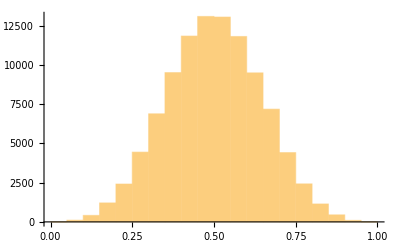

```mathematica
Table[(r+r+r+r)/4, {10^5}] // Histogram
```

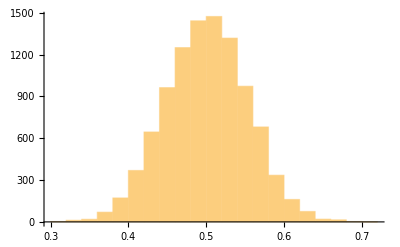

```mathematica
Table[RandomVariate[UniformDistribution[], 30] // Mean, {10^4}] // Histogram
```

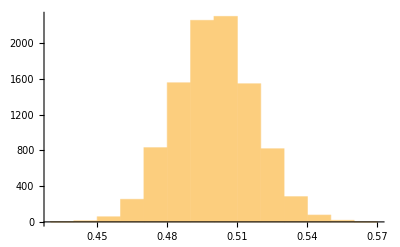

```mathematica
Table[RandomVariate[UniformDistribution[], 300] // Mean, {10^4}] // Histogram
```

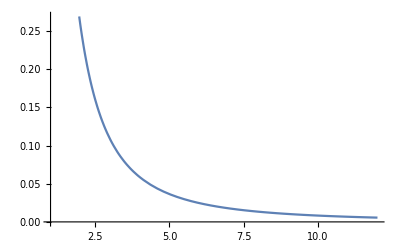

```mathematica
Plot[PDF[ParetoDistribution[1,1.14],x],{x, 1,12}]
```

545.871

8.14286

32.7854

8.14286

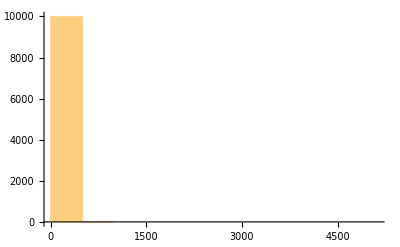

17.4681

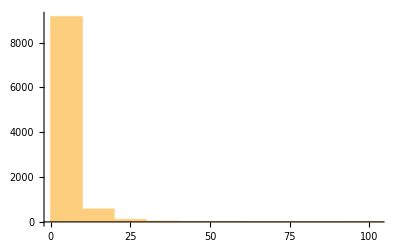

```mathematica
RandomVariate[ParetoDistribution[1,1.14],30]// Max

ParetoDistribution[1,1.14]//Mean
```

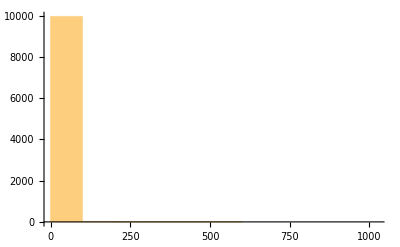

```mathematica
Histogram[Table[RandomVariate[ParetoDistribution[1,1.14],30]// Mean, {10^4}], 50]
```